# Análise dos Fusos

Falta organizar com calma quais dados eu vou usar nas correlações

Salvar os dados de Velocidade

Arquivos:  ok1 (Pacientes saudáveis)

Carrega Pacotes Úteis

```mathematica
Needs["ErrorBarPlots`"]
```

Define Variáveis Úteis para as análises e lê algumas imagens.

```mathematica
prefix="/Users/neylemke/alunos/Inhonho/";
$HistoryLength=0;
```

Define algumas funções para determinar a origem dos fusos por triangulação.

```mathematica
Fthres=13;
gap=0.25;
nchannels=8;
```

Lê os dados e gera o dataset.

```mathematica
csv=Import[prefix<>"TheSpindleOneTableOSAv01.csv"];
csv2=Import[prefix<>"TheSpindleOneTableV05.csv"];
csvpacientes=Import[prefix<>"tabela-clinica-osas.dat"];
```

```mathematica
dataset1=geraDataset[csv];
dataset2=geraDataset[csv2];
dataset=Union[dataset1,dataset2];
dataset=Select[dataset,#Examindexglob≠70502&];
datasetpacientes=geraDataset[csvpacientes];
lisexames=datasetpacientes[All,"Exame"];
partpacientes=GroupBy[dataset,"Examindexglob"];
fastSpindles=Select[dataset,#FreqSSglob≥Fthres&];
slowSpindles=Select[dataset,!(#FreqSSglob≥Fthres)&];
posSpindles=Select[dataset,#ChirpSSglob>=0&];
negSpindles=Select[dataset,!(#ChirpSSglob>=0)&];
```

```mathematica
varlist={"rKOPglob","TKOPglob","mKOPglob","ChirpSSglob","FreqSSglob","IduracPropglob"};
lisnamesCol={"Control", "OSA"};
```

{r,T (s),m  (s),Chirp  (Hz/s),Frequency  (Hz),Duration (s)}

/Users/neylemke/alunos/Inhonho/tabsyncall.tex

```mathematica
tabiah=geralinhaiah[dataset,datasetpacientes,#]&/@varlist;
tabiahTex=corrigeAcentos@ geratabiahTex[tabiah,assocVarUnits/@varlist,lisnamesCol];
Export[prefix<>"tabsyncall.tex",tabiahTex,"String"]
compilaTex[tabiahTex,"/Users/neylemke/Luisa/BancodeDadosDoutorado/"]
```

-Graphics-

```mathematica
tabiah=geralinhaiah[slowSpindles,datasetpacientes,#]&/@varlist;
tabiahTex=corrigeAcentos@ geratabiahTex[tabiah,assocVarUnits/@varlist,lisnamesCol];
compilaTex[tabiahTex,prefix="/Users/neylemke/Luisa/BancodeDadosDoutorado/"]
```

-Graphics-

```mathematica
tabiah=geralinhaiah[fastSpindles,datasetpacientes,#]&/@varlist;
tabiahTex=corrigeAcentos@ geratabiahTex[tabiah,assocVarUnits/@varlist,lisnamesCol];
compilaTex[tabiahTex,prefix="/Users/neylemke/Luisa/BancodeDadosDoutorado/"]
```

-Graphics-

```mathematica
tabiah=geralinhaiah[posSpindles,datasetpacientes,#]&/@varlist;
tabiahTex=corrigeAcentos@ geratabiahTex[tabiah,assocVarUnits/@varlist,lisnamesCol];
compilaTex[tabiahTex,prefix="/Users/neylemke/Luisa/BancodeDadosDoutorado/"]
```

-Graphics-

```mathematica
tabiah=geralinhaiah[negSpindles,datasetpacientes,#]&/@varlist;
tabiahTex=corrigeAcentos@ geratabiahTex[tabiah,assocVarUnits/@varlist,lisnamesCol];
compilaTex[tabiahTex,prefix="/Users/neylemke/Luisa/BancodeDadosDoutorado/"]
```

-Graphics-

```mathematica
tabiah=geralinhaiah[posSpindles,datasetpacientes,#]&/@varlist;
tabiahTex=corrigeAcentos@ geratabiahTex[tabiah,assocVarUnits/@varlist,lisnamesCol];
compilaTex[tabiahTex,prefix="/Users/neylemke/Luisa/BancodeDadosDoutorado/"]
```

```mathematica
lisiah=Table[{Mean[partpacientes[[i]][All,"mKOPglob"]],First@Normal@(Select[datasetpacientes,#Exame==Keys[partpacientes][[i]]&])[All,"IAH"]},{i,1,Length[partpacientes]}];
lm=LinearModelFit[lisiah,x,x];
lm["ParameterConfidenceIntervals"]
lm["BestFitParameters"]
lm["ParameterPValues"]
lis1=Select[lisiah,Last[#]>=5&];
lis2=Select[lisiah,Last[#]<5&];

LocationTest[{First/@lis1,First/@lis2}]
```

{{23.0782,86.8231},{-75.8478,-7.06501}}

{54.9507,-41.4564}

{0.00139649,0.019791}

1.49856×10^-6

```mathematica
lisiah=Table[{Mean[partpacientes[[i]][All,"mKOPglob"]],First@Normal@(Select[datasetpacientes,#Exame==Keys[partpacientes][[i]]&])[All,"IAHrem"]},{i,1,Length[partpacientes]}];
lm=LinearModelFit[lisiah,x,x];
lm["ParameterConfidenceIntervals"]
lm["BestFitParameters"]
lm["ParameterPValues"]
lis1=Select[lisiah,Last[#]>=5&];
lis2=Select[lisiah,Last[#]<5&];
LocationTest[{First/@lis1,First/@lis2}]
```

```mathematica
lisiah=Table[{Mean[partpacientes[[i]][All,"mKOPglob"]],First@Normal@(Select[datasetpacientes,#Exame==Keys[partpacientes][[i]]&])[All,"IndexR"]},{i,1,Length[partpacientes]}];
lm=LinearModelFit[lisiah,x,x];
lm["ParameterConfidenceIntervals"]
lm["BestFitParameters"]
lm["ParameterPValues"]
lis1=Select[lisiah,Last[#]>=5&];
lis2=Select[lisiah,Last[#]<5&];
LocationTest[{First/@lis1,First/@lis2}]
```

{{2.40287,93.7179},{-78.4112,20.1207}}

{48.0604,-29.1452}

{0.03976,0.236413}

0.586447

```mathematica
lisiah=Table[{Mean[partpacientes[[i]][All,"mKOPglob"]],First@Normal@(Select[datasetpacientes,#Exame==Keys[partpacientes][[i]]&])[All,"IndexR"]},{i,1,Length[partpacientes]}];
lm=LinearModelFit[lisiah,x,x];
lm["ParameterConfidenceIntervals"]
lm["BestFitParameters"]
lm["ParameterPValues"]
lis1=Select[lisiah,Last[#]>=5&];
lis2=Select[lisiah,Last[#]<5&];
LocationTest[{First/@lis1,First/@lis2}]
```

```mathematica
lisiah=Table[{Mean[partpacientes[[i]][All,"mKOPglob"]],First@Normal@(Select[datasetpacientes,#Exame==Keys[partpacientes][[i]]&])[All,"epworth"]},{i,1,Length[partpacientes]}];
lm=LinearModelFit[lisiah,x,x];
lm["ParameterConfidenceIntervals"]
lm["BestFitParameters"]
lm["ParameterPValues"]
lis1=Select[lisiah,Last[#]>=5&];
lis2=Select[lisiah,Last[#]<5&];
LocationTest[{First/@lis1,First/@lis2}]
```

LinearModelFit::notdata: The first argument is not a vector, matrix, or a list containing a design matrix and response vector.

LinearModelFit[{{0.677921,11},{0.772924,2},{0.776546,17},{0.981783,2},{1.12796,15},{0.709394,14},{1.25759,10},{1.00744,10},{0.80272,1},{0.927056,13},{0.725474,11},{1.10069,6},{0.887496,14},{0.902954,7},{0.885319,13},{0.87324,21},{0.878071,15},{1.2604,14},{1.05636,10},{0.900534,10},{1.25596,19},{0.807242,18},{0.8601,xx},{1.17721,10},{0.872441,7},{0.763155,6},{0.841488,8},{0.735877,8},{0.722759,16},{0.845346,18},{0.880808,12},{0.921989,11}},x,x][ParameterConfidenceIntervals]

LinearModelFit[{{0.677921,11},{0.772924,2},{0.776546,17},{0.981783,2},{1.12796,15},{0.709394,14},{1.25759,10},{1.00744,10},{0.80272,1},{0.927056,13},{0.725474,11},{1.10069,6},{0.887496,14},{0.902954,7},{0.885319,13},{0.87324,21},{0.878071,15},{1.2604,14},{1.05636,10},{0.900534,10},{1.25596,19},{0.807242,18},{0.8601,xx},{1.17721,10},{0.872441,7},{0.763155,6},{0.841488,8},{0.735877,8},{0.722759,16},{0.845346,18},{0.880808,12},{0.921989,11}},x,x][BestFitParameters]

LinearModelFit[{{0.677921,11},{0.772924,2},{0.776546,17},{0.981783,2},{1.12796,15},{0.709394,14},{1.25759,10},{1.00744,10},{0.80272,1},{0.927056,13},{0.725474,11},{1.10069,6},{0.887496,14},{0.902954,7},{0.885319,13},{0.87324,21},{0.878071,15},{1.2604,14},{1.05636,10},{0.900534,10},{1.25596,19},{0.807242,18},{0.8601,xx},{1.17721,10},{0.872441,7},{0.763155,6},{0.841488,8},{0.735877,8},{0.722759,16},{0.845346,18},{0.880808,12},{0.921989,11}},x,x][ParameterPValues]

0.570082

1.49856×10^-6

```mathematica
lisiah=Table[{Mean[partpacientes[[i]][All,"t0KOPglob"]],First@Normal@(Select[datasetpacientes,#Exame==Keys[partpacientes][[i]]&])[All,"IAH"]},{i,1,Length[partpacientes]}];
lm=LinearModelFit[lisiah,x,x];
lm["ParameterConfidenceIntervals"]
lm["BestFitParameters"]
lis1=Select[lisiah,Last[#]>=5&];
lis2=Select[lisiah,Last[#]<5&];
LocationTest[{First/@lis1,First/@lis2}]
```

{{16.8902,39.7397},{-118.491,-7.06704}}

{28.3149,-62.7789}

0.000686409

```mathematica
lisiah=Table[{Mean[partpacientes[[i]][All,"ChirpSSglob"]],First@Normal@(Select[datasetpacientes,#Exame==Keys[partpacientes][[i]]&])[All,"IAH"]},{i,1,Length[partpacientes]}];
lm=LinearModelFit[lisiah,x,x];
lm["ParameterConfidenceIntervals"]
lm["BestFitParameters"]
lis1=Select[lisiah,Last[#]>=5&];
lis2=Select[lisiah,Last[#]<5&];
LocationTest[{First/@lis1,First/@lis2}]
```

{{-6.89307,16.3576},{-83.6825,-8.14089}}

{4.73225,-45.9117}

0.273439

```mathematica
lisiah=Table[{Mean[partpacientes[[i]][All,"DuracPropglob"]],First@Normal@(Select[datasetpacientes,#Exame==Keys[partpacientes][[i]]&])[All,"IAH"]},{i,1,Length[partpacientes]}];
lm=LinearModelFit[lisiah,x,x];
lm["ParameterConfidenceIntervals"]
lm["BestFitParameters"]
lis1=Select[lisiah,Last[#]>=5&];
lis2=Select[lisiah,Last[#]<5&];
LocationTest[{First/@lis1,First/@lis2}]
```

{{-94.1415,68.5947},{-180.013,390.094}}

{-12.7734,105.04}

0.192779

```mathematica
lisiah=Table[{Mean[partpacientes[[i]][All,"rKOPglob"]],First@Normal@(Select[datasetpacientes,#Exame==Keys[partpacientes][[i]]&])[All,"IAH"]},{i,1,Length[partpacientes]}];
lm=LinearModelFit[lisiah,x,x];
lm["ParameterConfidenceIntervals"]
lm["BestFitParameters"]
lis1=Select[lisiah,Last[#]>=5&];
lis2=Select[lisiah,Last[#]<5&];
LocationTest[{First/@lis1,First/@lis2}]
```

{{-180.562,306.65},{-303.237,207.027}}

{63.0443,-48.1054}

0.860064

Separa os fusos em lentos e rápidos.

```mathematica
fastSpindles=Select[dataset,#FreqSSglob≥Fthres&];
slowSpindles=Select[dataset,!(#FreqSSglob≥Fthres)&];
```

```mathematica
TableForm[header]
```

Examindexglob
SSindexglob
rKOPglob
TKOPglob
mKOPglob
t0KOPglob
r2KOPglob
ChirpSSf3
ChirpSSf4
ChirpSSc3
ChirpSSc4
ChirpSSp3
ChirpSSp4
ChirpSSo1
ChirpSSo2
ChirpSSglob
FreqSSf3
FreqSSf4
FreqSSc3
FreqSSc4
FreqSSp3
FreqSSp4
FreqSSo1
FreqSSo2
FreqSSglob
TimePropf3f4
TimePropf3c3
TimePropf3c4
TimePropf3p3
TimePropf3p4
TimePropf3o1
TimePropf3o2
TimePropf4c3
TimePropf4c4
TimePropf4p3
TimePropf4p4
TimePropf4o1
TimePropf4o2
TimePropc3c4
TimePropc3p3
TimePropc3p4
TimePropc3o1
TimePropc3o2
TimePropc4p3
TimePropc4p4
TimePropc4o1
TimePropc4o2
TimePropp3p4
TimePropp3o1
TimePropp3o2
TimePropp4o1
TimePropp4o2
TimePropo1o2
VelocPropglob
TimelocPropglob
EnvmaxPropf3
EnvmaxPropf4
EnvmaxPropc3
EnvmaxPropc4
EnvmaxPropp3
EnvmaxPropp4
EnvmaxPropo1
EnvmaxPropo2
DuracPropf3
DuracPropf4
DuracPropc3
DuracPropc4
DuracPropp3
DuracPropp4
DuracPropo1
DuracPropo2
DuracPropglob
IduracPropf3
IduracPropf4
IduracPropc3
IduracPropc4
IduracPropp3
IduracPropp4
IduracPropo1
IduracPropo2
IduracPropglob
TimemaxPropf3
TimemaxPropf4
TimemaxPropc3
TimemaxPropc4
TimemaxPropp3
TimemaxPropp4
TimemaxPropo1
TimemaxPropo2
DeltafracFreqf3
DeltafracFreqf4
DeltafracFreqc3
DeltafracFreqc4
DeltafracFreqp3
DeltafracFreqp4
DeltafracFreqo1
DeltafracFreqo2

## Gera as Velocidades

```mathematica
lischannelspos={{0.04000000000000001,-0.045000000000000005,0.036},{-0.039400000000000004,-0.045500000000000006,0.0365},{0.05560000000000001,0.018,0.043000000000000003},{-0.05430000000000001,0.018,0.043300000000000005},{0.040600000000000004,0.073,0.033},{-0.03900000000000001,0.073,0.033},{0.026900000000000004,0.1,-0.020000000000000004},{-0.0256,0.1,-0.020000000000000004}};
listemp=Table[
delays=ParallelTable[If[i<j,dataset[k,"TimeProp"<>lischannels[[i]]<>lischannels[[j]]],0],{i,1,8},{j,1,8}];
lisdist=Table[Norm[(lischannelspos[[i]]-{x,y,z})],{i,1,nchannels}];
eq=Sum[((lisdist[[i]]-lisdist[[j]])/Abs[v]-delays[[i,j]])^2,{j,2,8},{i,1,j-1}];
NMinimize[{eq,x^2/(0.05)^2+y^2/(0.1)^2+z^2/(0.05)^2<1&&z>-0.06&&z<0.04 &&v>0.01&&v<1.0},{x,y,{z,-0.03,0.02},v}],{k,1,Length[dataset]}];
lis3D=Table[{{{x,y,z},v}/.listemp[[i,2]],listemp[[i,1]]},{i,1,Length[dataset]}];
```

```mathematica
dataset2=Dataset[MapThread[Append,{Normal[dataset],Thread["error"->(Last/@ lis3D)]}]];
dataset2=Dataset[MapThread[Append,{Normal[dataset2],Thread["pos"->(First/@(First/@ lis3D))]}]];
dataset2=Dataset[MapThread[Append,{Normal[dataset2],Thread["vel"->(Last/@(First/@ lis3D))]}]];fastSpindles=Select[dataset2,#FreqSSglob≥Fthres&];
slowSpindles=Select[dataset2,!(#FreqSSglob≥Fthres)&];
dataset3=dataset2[Select[#error<1&&#vel<1.0&]];
```

## Consistência

Freq

```mathematica
lisdata=lisFreq;
dataname="Frequency";
corrTab=Table[Correlation[Normal[dataset2[All,lisdata[[i]]]],Normal[dataset2[All,lisdata[[j]]]]],{i,1,8},{j,1,8}];
pvaluecorrTab=Table[CorrelationTest[Transpose[{Normal[dataset2[All,lisdata[[i]]]],Normal[dataset2[All,lisdata[[j]]]]}]],{i,1,8},{j,1,8}];
pvaluecorrTab=Table[CorrelationTest[Transpose[{Normal[dataset2[All,lisdata[[i]]]],Normal[dataset2[All,lisdata[[j]]]]}]],{i,1,8},{j,1,8}];
pvaluecorrRandomTab=Table[CorrelationTest[Transpose[{Normal[dataset2[All,lisFreq[[i]]]],RandomSample[Normal[dataset2[All,lisFreq[[j]]]]]}]],{i,1,8},{j,1,8}];
TableForm[pvaluecorrTab,opts]
TableForm[corrTab,opts]
Export[prefix<>"figures/corr"<>dataname<>"TabTex.txt",geraCorrTabTex[corrTab,lisdata]];
Export[prefix<>"figures/pvaluecorr"<>dataname<>"TabTex.txt",gerapvalueCorrTabTex[pvaluecorrTab,lisdata]];
Export[prefix<>"figures/pvaluecorrRandom"<>dataname<>"TabTex.txt",gerapvalueCorrTabTex[pvaluecorrTab,lisdata]];
Export[prefix<>"figures/corr"<>dataname<>"Channels.png",geraCorrSmoothChannels[lisdata]];
```

| f3 | f4 | c3 | c4 | p3 | p4 | o1 | o2
f3 | 0. | 4.14149×10^-43 | 5.20717×10^-53 | 1.38517×10^-32 | 2.99567×10^-25 | 6.12036×10^-23 | 3.21209×10^-20 | 6.73194×10^-18
f4 | 4.14149×10^-43 | 0. | 4.65019×10^-32 | 2.04489×10^-62 | 5.56753×10^-21 | 1.35406×10^-26 | 7.68119×10^-25 | 8.83041×10^-21
c3 | 5.20717×10^-53 | 4.65019×10^-32 | 0. | 1.44776×10^-65 | 5.48498×10^-97 | 1.42421×10^-57 | 4.20574×10^-43 | 2.3025×10^-43
c4 | 1.38517×10^-32 | 2.04489×10^-62 | 1.44776×10^-65 | 0. | 1.21875×10^-58 | 9.9635×10^-124 | 2.05816×10^-50 | 3.02404×10^-53
p3 | 2.99567×10^-25 | 5.56753×10^-21 | 5.48498×10^-97 | 1.21875×10^-58 | 0. | 4.96306×10^-83 | 1.55496×10^-81 | 1.64953×10^-63
p4 | 6.12036×10^-23 | 1.35406×10^-26 | 1.42421×10^-57 | 9.9635×10^-124 | 4.96306×10^-83 | 1.01736291670703×10^-55611 | 3.80235×10^-67 | 1.22042×10^-116
o1 | 3.21209×10^-20 | 7.68119×10^-25 | 4.20574×10^-43 | 2.05816×10^-50 | 1.55496×10^-81 | 3.80235×10^-67 | 0. | 4.86397×10^-123
o2 | 6.73194×10^-18 | 8.83041×10^-21 | 2.3025×10^-43 | 3.02404×10^-53 | 1.64953×10^-63 | 1.22042×10^-116 | 4.86397×10^-123 | 1.01736291670703×10^-55611

| f3 | f4 | c3 | c4 | p3 | p4 | o1 | o2
f3 | 1. | 0.447544 | 0.497338 | 0.394437 | 0.352128 | 0.342612 | 0.314871 | 0.293966
f4 | 0.447544 | 1. | 0.389821 | 0.543024 | 0.310192 | 0.379312 | 0.354405 | 0.328039
c3 | 0.497338 | 0.389821 | 1. | 0.507503 | 0.577927 | 0.479411 | 0.426833 | 0.431341
c4 | 0.394437 | 0.543024 | 0.507503 | 1. | 0.488746 | 0.67892 | 0.492299 | 0.490122
p3 | 0.352128 | 0.310192 | 0.577927 | 0.488746 | 1. | 0.573664 | 0.561672 | 0.518259
p4 | 0.342612 | 0.379312 | 0.479411 | 0.67892 | 0.573664 | 1. | 0.536019 | 0.65739
o1 | 0.314871 | 0.354405 | 0.426833 | 0.492299 | 0.561672 | 0.536019 | 1. | 0.683312
o2 | 0.293966 | 0.328039 | 0.431341 | 0.490122 | 0.518259 | 0.65739 | 0.683312 | 1.

StringJoin::string: String expected at position 2 in « 1 ».

StringJoin::string: String expected at position 4 in « 1 ».

StringJoin::string: String expected at position 2 in « 1 ».

General::stop: Further output of StringJoin :: string will be suppressed during this calculation.

StringJoin::string: String expected at position 2 in « 1 ».

StringJoin::string: String expected at position 4 in « 1 ».

StringJoin::string: String expected at position 2 in « 1 ».

General::stop: Further output of StringJoin :: string will be suppressed during this calculation.

Duration

```mathematica
lisdata=lisDura;
dataname="Duration";
corrTab=Table[Correlation[Normal[dataset2[All,lisdata[[i]]]],Normal[dataset2[All,lisdata[[j]]]]],{i,1,8},{j,1,8}];
pvaluecorrTab=Table[CorrelationTest[Transpose[{Normal[dataset2[All,lisdata[[i]]]],Normal[dataset2[All,lisdata[[j]]]]}]],{i,1,8},{j,1,8}];
Export[prefix<>"figures/corr"<>dataname<>"TabTex.txt",geraCorrTabTex[corrTab,lisdata]];
TableForm[pvaluecorrTab,TableHeadings->{Style[#,FontFamily->"Times",18]&/@lischannels,Style[#,FontFamily->"Times",18]&/@lischannels},TableAlignments->Center]
Export[prefix<>"figures/corr"<>dataname<>"Channels.png",geraCorrSmoothChannels[lisdata]];
```

| f3 | f4 | c3 | c4 | p3 | p4 | o1 | o2
f3 | 1.01736291670703×10^-55611 | 6.07213×10^-25 | 2.13457×10^-84 | 2.4214×10^-28 | 5.65849×10^-33 | 1.37445×10^-24 | 1.85859×10^-17 | 3.81315×10^-15
f4 | 6.07213×10^-25 | 0. | 3.14662×10^-19 | 1.80995×10^-47 | 1.84888×10^-12 | 2.12598×10^-22 | 1.19747×10^-12 | 1.94097×10^-10
c3 | 2.13457×10^-84 | 3.14662×10^-19 | 0. | 3.03658×10^-60 | 1.47243×10^-164 | 8.37977×10^-69 | 9.36945×10^-53 | 7.89104×10^-35
c4 | 2.4214×10^-28 | 1.80995×10^-47 | 3.03658×10^-60 | 0. | 4.43359×10^-53 | 1.12359×10^-184 | 4.44778×10^-38 | 4.94226×10^-54
p3 | 5.65849×10^-33 | 1.84888×10^-12 | 1.47243×10^-164 | 4.43359×10^-53 | 1.01736291670703×10^-55611 | 3.48254×10^-95 | 1.13917×10^-116 | 1.81398×10^-67
p4 | 1.37445×10^-24 | 2.12598×10^-22 | 8.37977×10^-69 | 1.12359×10^-184 | 3.48254×10^-95 | 0. | 6.83306×10^-78 | 2.31596×10^-122
o1 | 1.85859×10^-17 | 1.19747×10^-12 | 9.36945×10^-53 | 4.44778×10^-38 | 1.13917×10^-116 | 6.83306×10^-78 | 0. | 1.85071×10^-127
o2 | 3.81315×10^-15 | 1.94097×10^-10 | 7.89104×10^-35 | 4.94226×10^-54 | 1.81398×10^-67 | 2.31596×10^-122 | 1.85071×10^-127 | 0.

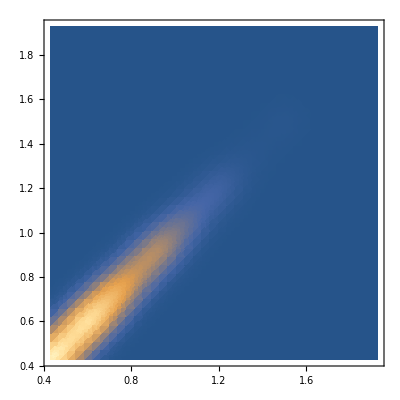
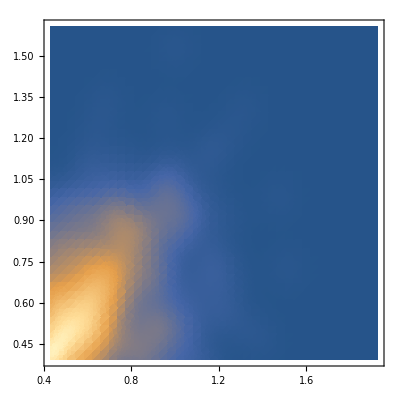
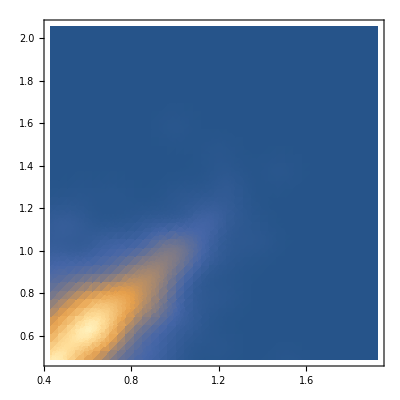
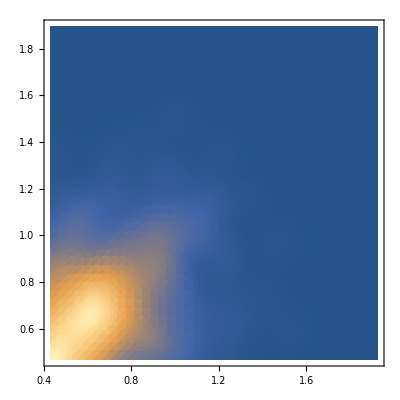
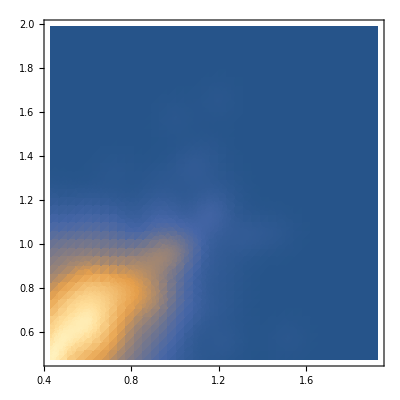
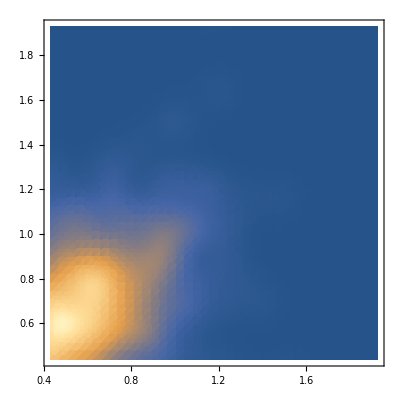
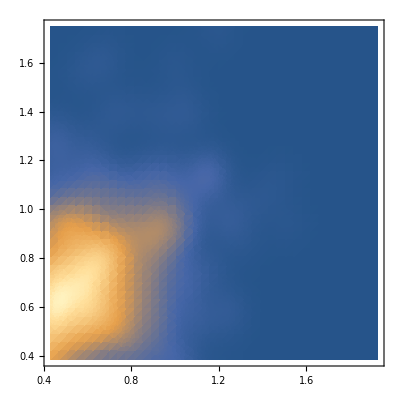
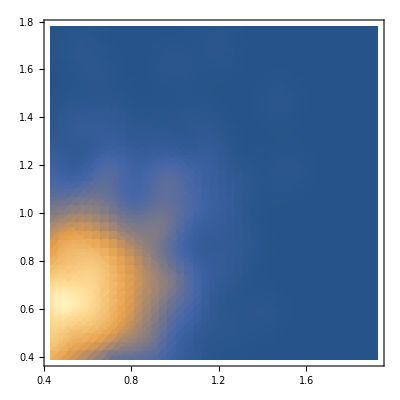
| f3 | f4 | c3 | c4 | p3 | p4 | o1 | o2
f3 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
f4 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
c3 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
c4 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
p3 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
p4 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
o1 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
o2 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
geraCorrSmoothChannels[lisdata]
```

Chirp

```mathematica
lisdata=lisChirp;
dataname="Chirp";
corrTab=Table[Correlation[Normal[dataset2[All,lisdata[[i]]]],Normal[dataset2[All,lisdata[[j]]]]],{i,1,8},{j,1,8}];
pvaluecorrTab=Table[CorrelationTest[Transpose[{Normal[dataset2[All,lisdata[[i]]]],Normal[dataset2[All,lisdata[[j]]]]}]],{i,1,8},{j,1,8}];
TableForm[pvaluecorrTab,opts]
Export[prefix<>"figures/corr"<>dataname<>"TabTex.txt",geraCorrTabTex[corrTab,lisdata]];
Export[prefix<>"figures/corr"<>dataname<>"Channels.png",geraCorrSmoothChannels[lisdata]];
```

| f3 | f4 | c3 | c4 | p3 | p4 | o1 | o2
f3 | 0. | 3.58817×10^-66 | 5.1044×10^-161 | 9.46791×10^-57 | 5.69117×10^-58 | 2.82385×10^-37 | 1.04661×10^-27 | 7.18913×10^-26
f4 | 3.58817×10^-66 | 0. | 3.82458×10^-40 | 1.21537×10^-121 | 1.16658×10^-23 | 2.49898×10^-50 | 3.78483×10^-19 | 7.29587×10^-25
c3 | 5.1044×10^-161 | 3.82458×10^-40 | 0. | 4.33012×10^-72 | 7.2592×10^-206 | 2.105×10^-69 | 4.79574×10^-68 | 2.27588×10^-45
c4 | 9.46791×10^-57 | 1.21537×10^-121 | 4.33012×10^-72 | 0. | 1.76375×10^-59 | 1.14131×10^-243 | 4.17378×10^-39 | 4.04138×10^-65
p3 | 5.69117×10^-58 | 1.16658×10^-23 | 7.2592×10^-206 | 1.76375×10^-59 | 0. | 3.12673×10^-91 | 2.70277×10^-132 | 2.3325×10^-75
p4 | 2.82385×10^-37 | 2.49898×10^-50 | 2.105×10^-69 | 1.14131×10^-243 | 3.12673×10^-91 | 0. | 4.84171×10^-75 | 7.06951×10^-161
o1 | 1.04661×10^-27 | 3.78483×10^-19 | 4.79574×10^-68 | 4.17378×10^-39 | 2.70277×10^-132 | 4.84171×10^-75 | 0. | 1.96714×10^-156
o2 | 7.18913×10^-26 | 7.29587×10^-25 | 2.27588×10^-45 | 4.04138×10^-65 | 2.3325×10^-75 | 7.06951×10^-161 | 1.96714×10^-156 | 0.

```mathematica
geraCorrSmoothChannels[lisdata]
```

| f3 | f4 | c3 | c4 | p3 | p4 | o1 | o2
f3 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
f4 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
c3 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
c4 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
p3 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
p4 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
o1 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
o2 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

## Análise Local

```mathematica
var=lisChirp;
meanChirp=Join[Table[lisdata=Normal[slowSpindles[All,var[[i]]]];
{lischannels[[i]],Mean[lisdata],LocationTest[lisdata]},{i,1,8}],
Table[lisdata=Normal[fastSpindles[All,var[[i]]]];
{lischannels[[i]],Mean[lisdata],LocationTest[lisdata]},{i,1,8}]];
```

```mathematica
lisnamesRow={""," ", " "," "," Slow"," ", " "," "," ", " "," "," ","Fast"," ", " "," "};
lisnamesCol={"SS Type", "Channel","Mean Chirp","p-value"};
headerString=StringTake[StringJoin[( #<>" & "&/@ lisnamesCol)],{1,-3}]<>"\\\\\n \\midrule\n ";
colString="l"<>StringJoin[Table["c",{i,1,Length[meanChirp[[1]]]}]];tabChirpTex="\n\n\\begin{tabular}{"<>colString<>"}\n\\toprule\n"<> headerString<>StringJoin[Table[StringJoin[" "<>lisnamesRow[[i]], " & "<>meanChirp[[i,1]]<> Table[" & \\nprounddigits{3}\\numprint{"<> ToString[CForm[meanChirp[[i,j]]]]<>"}",{j,2,Length[meanChirp[[1]]]}]]<> "\\\\\n",{i,1,Length[meanChirp]}]]<>" \\bottomrule\n\\end{tabular}";
Export[prefix<>"/figures/tabChirp.txt",tabChirpTex]
```

/Users/rafaeltoledo/Documents/MATLAB/Codigos EEG/ExamesTotal/ok1//figures/tabChirp.txt

```mathematica
"/Users/rafaeltoledo/Documents/MATLAB/Codigos EEG/ExamesTotal/ok1//figures/tabChirp.txt"
```

## Médias e Histogramas

```mathematica
histosPlotList={};
```

```mathematica
var="FreqSSglob";
binsize=0.125;
list=HistogramList[dataset[All,var],{binsize},"Probability"];
list=Transpose[{Delete[list[[1]],-1]-binsize,list[[2]]}];
f=Interpolation[list,InterpolationOrder->5];
gr1=Plot[f[x]/binsize,{x,11.7,13},Filling->Bottom,PlotRange->{{11.,15},{0,0.12/binsize}},PlotStyle->{Orange,Thickness[0.01]},FrameLabel->{Style["Frequency (Hz)",14],Style["Probability",14]},Frame->True];
gr2=Plot[f[x]/binsize,{x,13,14.75},Filling->Bottom,PlotStyle->{Red,Thickness[0.01]}];
freqPlot=Show[gr1,gr2,Epilog->{Inset[Style["A",24,Background->White],Scaled[{0.07,0.9
}]],Inset[Style[Framed["Slow"],14,Background->White],{11.7,0.08/binsize}],Inset[Style[Framed["Fast"],14,Background->White],{14.3,0.08/binsize}],Dashed,Line[{{13,0},{13,0.12/binsize}}]},ImageSize->Medium]
histosPlotList=Append[histosPlotList,freqPlot];
```

-Graphics-

```mathematica
fastSpindles=Select[dataset,#FreqSSglob≥Fthres&];
slowSpindles=Select[dataset,!(#FreqSSglob≥Fthres)&];
var="ChirpSSglob";
dataslow=slowSpindles[All,var];
binsize=0.3;
list=HistogramList[dataslow,{binsize},"Probability"];
list=Transpose[{Delete[list[[1]],-1]+binsize/2,list[[2]]}];
g=Interpolation[list,InterpolationOrder->3];
datafast=fastSpindles[All,var];
list=HistogramList[datafast,{binsize},"Probability"];
list=Transpose[{Delete[list[[1]],-1]+binsize/2,list[[2]]}];
f=Interpolation[list,InterpolationOrder->3];
chirpPlot=ListPlot[{Append[Table[{f[x]-0.001,x},{x,Min[datafast]+0.0,Max[datafast],.1}],{0,Max[datafast]}],Append[Table[{-g[x]+0.001,x},{x,Min[dataslow]-0.015,Max[dataslow],0.1}],{.0,Max[dataslow]}]},Joined->True,Filling->Axis,PlotStyle->{{Red,Thickness[0.01]},{Orange,Thickness[0.01]}},FrameLabel->{Style["Probability",14],Style["Chirp (Hz/s)",14]},Frame->True,AxesOrigin->{0,0.},Axes->False,Epilog->{Thickness[0.007],Line[{{0,-2},{0,1.5}}],Dashed,Thickness[0.003],Line[{{0,Mean[fastSpindles[All,var]]},{0.22,Mean[fastSpindles[All,var]]}}],Line[{{0,Mean[slowSpindles[All,var]]},{-0.25,Mean[slowSpindles[All,var]]}}],
Inset[Style["B",24,Background->White],Scaled[{0.07,0.9}]],Inset[Style[Framed["Slow"],14,Background->White],{-0.1,Mean[slowSpindles[All,var]]}],Inset[Style[Framed["Fast"],14,Background->White],{0.1,Mean[fastSpindles[All,var]]}]},ImageSize->Medium]
histosPlotList=Append[histosPlotList,chirpPlot];
```

InterpolatingFunction::dmval: Input value {-1.66875} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

Rule::argr: Rule called with 1 argument; 2 arguments are expected.

```mathematica
axisFlip=#/.{x_Line|x_GraphicsComplex:>MapAt[#~Reverse~2&,x,1],x:(PlotRange->_):>x~Reverse~2}&;
```

```mathematica
var="ChirpSSglob";
dataslow=slowSpindles[All,var];
datafast=fastSpindles[All,var];
gr=SmoothHistogram[dataslow,0.3,PlotRange->{{-2.5,2},{-2.5,2.5}},Filling->Axis,PlotStyle->{Orange,Thickness[0.01]}];
gr[[1,2,1]]=gr[[1,2,1]]/.{x_,y_}->{-y,x};
Show[{
axisFlip[SmoothHistogram[datafast,0.3,PlotRange->{{-2.5,2},{-1,1}},Filling->Axis,PlotStyle->{Red,Thickness[0.01]}]],gr},FrameLabel->{Style["Probability",14],Style["Chirp (Hz/s)",14]},Frame->True,AxesOrigin->{0,0.},Axes->False,Epilog->{Thickness[0.007],Line[{{0,-2.5},{0,2.0}}],Dashed,Thickness[0.003],Line[{{0,Mean[fastSpindles[All,var]]},{0.65,Mean[fastSpindles[All,var]]}}],Line[{{0,Mean[slowSpindles[All,var]]},{-0.68,Mean[slowSpindles[All,var]]}}],
Inset[Style["B",24,Background->White],Scaled[{0.07,0.9}]],Inset[Style[Framed["Slow"],14,Background->White],{-0.2,Mean[slowSpindles[All,var]]}],Inset[Style[Framed["Fast"],14,Background->White],{0.2,Mean[fastSpindles[All,var]]}]},ImageSize->Medium]
```

-Graphics-

```mathematica
var="vel";
binsize=0.02;
dataplot=dataset2[All,var];
gr1=SmoothHistogram[dataplot,binsize,PlotRange->All,Filling->Axis,
PlotStyle->{Orange,Thickness[0.01]},Axes->False,FrameLabel->{Style["Velocity (m/s)",14],Style["Probability",14]},Frame->True];
velPlot=Show[gr1,Epilog->{Inset[Style["C",24,Background->White],Scaled[{0.07,0.9}]],Dashed,Line[{{13,0},{13,0.12}}]},ImageSize->Medium]
(* histosPlotList=Append[histosPlotList,velPlot];*)
```

-Graphics-

```mathematica
var="TKOPglob";
binsize=0.02;
dataplot=dataset2[All,var];
gr1=SmoothHistogram[dataplot,binsize, PlotRange->{{0,1},{0,8}},Filling->Axis,
PlotStyle->{Orange,Thickness[0.01]},Axes->False,PlotStyle->{Orange,Thickness[0.01]},FrameLabel->{Style["Synchronization Time (s)",14],Style["Probability",14]},Axes->False,Frame->True];
syncPlot=Show[gr1,Epilog->{Inset[Style["D",24,Background->White],Scaled[{0.07,0.9}]]},ImageSize->Medium]

histosPlotList=Append[histosPlotList,syncPlot];
```

-Graphics-

```mathematica
(*var="IduracPropglob";
binsize=0.05;
list=HistogramList[dataset2[All,var],{binsize},"Probability"];
list=Transpose[{Delete[list[[1]],-1]+binsize,list[[2]]}];
f=Interpolation[list,InterpolationOrder->5];
gr1=Plot[f[x],{x,0.015,1.2},Filling->Bottom,PlotRange->{{0.35,1.2},{0,0.15}},PlotStyle->{Orange,Thickness[0.01]},FrameLabel->{Style["Duration (s)",14],Style["Probability",14]},Frame->True];
durPlot=Show[gr1,Epilog->{Inset[Style["E",24,Background->White],Scaled[{0.07,0.9}]]},ImageSize->Medium]
histosPlotList=Append[histosPlotList,durPlot];*)
```

InterpolatingFunction::dmval: Input value {0.0150242} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

```mathematica
SmoothHistogram[RandomVariate[NormalDistribution[0,10],500]]
```

-Graphics-

```mathematica
Histogram[Normal[durfuso],{0.01},"Probability"]
```

-Graphics-

```mathematica
(*fastSpindles=Select[dataset,#FreqSSglob≥Fthres&];
slowSpindles=Select[dataset,!(#FreqSSglob≥Fthres)&];*)
var="mKOPglob";
binsize=0.15
dursync=dataset2[All,var]; (*Laranja*)
SmoothHistogram[dursync,binsize,PlotRange->{{0,2},{0,3}},Filling->Axis,
PlotStyle->{Orange,Thickness[0.01]},Axes->False,PlotStyle->{Orange,Thickness[0.01]},FrameLabel->{Style["Synchronization Time (s)",14],Style["Probability",14]},Axes->False,Frame->True];
var="IduracPropglob"; 
durfuso=dataset2[All,var]; (*Vermelho*)
gr=SmoothHistogram[dursync,binsize,PlotRange->{{-2.5,2.},{-2.5,2.5}},Filling->Axis,PlotStyle->{Orange,Thickness[0.01]}];
gr[[1,2,1]]=gr[[1,2,1]]/.{x_,y_}->{-y,x};
durPlot=Show[{
axisFlip[SmoothHistogram[durfuso,binsize,PlotRange->{{-0.,2.5},{-2.5,2.5}},Filling->Axis,PlotStyle->{Red,Thickness[0.01]}]],gr},
PlotStyle->{Orange,Thickness[0.01]},FrameLabel->{Style["Probability.10",14],Style["Time (s)",14]},Frame->True,AxesOrigin->{0,0.30},Axes->False,Epilog->{Thickness[0.007], Line[{{0,-2},{0,2.5}}],Dashed,Thickness[0.003],Line[{{0,Mean[durfuso]},{1.8,Mean[durfuso]}}],Line[{{0,Mean[dursync]},{-1.1,Mean[dursync]}}],
Inset[Style["E",24,Background->White],Scaled[{0.07,0.9}]],Inset[Style[Framed["m"],14,Background->White],{-0.3,Mean[dursync]}],Inset[Style[Framed["Duration"],14,Background->White],{0.55,Mean[durfuso]}]},ImageSize->Medium]
histosPlotList=Append[histosPlotList,durPlot];
```

0.15

-Graphics-

Rule::argr: Rule called with 1 argument; 2 arguments are expected.

```mathematica
var="rKOPglob";
lis=Normal[dataset[All,var]]/Max[dataset[All,var]];
Cum[x_]:=N[Length[Select[lis,#>x&]]/Length[lis]];
lis=Normal[slowSpindles[All,var]]/Max[dataset[All,var]];
Cumslow[x_]:=N[Length[Select[lis,#>x&]]/Length[lis]];
lis=Normal[fastSpindles[All,var]]/Max[dataset[All,var]];
Cumfast[x_]:=N[Length[Select[lis,#>x&]]/Length[lis]];
cumsumPlot=Plot[Cum[x],{x,0.5,1},PlotRange->{0,1.3},AxesLabel->{Style["r",18],Style["S(r)",18]},PlotStyle->{Thickness[0.01],Orange},FrameLabel->{Style["A",14],Style["Cumulative Sum",14]},Frame->True,Filling->Bottom,Epilog->{Inset[Style["F",24,Background->White],Scaled[{0.07,0.9}]],Dashed,Line[{{0.6,0.},{0.6,Cum[0.6]},{0,Cum[0.6]}}]},ImageSize->Medium]
histosPlotList=Append[histosPlotList,cumsumPlot];
```

-Graphics-

```mathematica
GraphicsGrid[Partition[histosPlotList,3]]
```

-Graphics-

```mathematica
Export[prefix<>"figures/histosPlot.pdf",GraphicsGrid[Partition[histosPlotList,3]]]
```

```mathematica
"/Users/rafaeltoledo/Documents/MATLAB/Codigos EEG/ExamesTotal/ok1/figures/histosPlot.pdf"
```

Relação entre Chirp e Frequência

```mathematica
dataFo=Table[dataset2[i,"FreqSSglob"]-dataset2[i,"mKOPglob"]*dataset2[i,"ChirpSSglob"]/2,{i,1,Length[dataset2]}];
```

```mathematica
binsize=0.125;
list=HistogramList[Table[dataset2[i,"FreqSSglob"]-dataset2[i,"IduracPropglob"]*dataset2[i,"ChirpSSglob"]/2,{i,1,Length[dataset2]}],{binsize},"Probability"];
list=Transpose[{Delete[list[[1]],-1]+binsize,list[[2]]}];
f=Interpolation[list,InterpolationOrder->5];
gr1=Plot[f[x],{x,12,15},Filling->Bottom,PlotRange->{{11,16.},{0,0.15}},PlotStyle->{Orange,Thickness[0.01]},FrameLabel->{Style["Duration (s)",14],Style["Probability",14]},Frame->True];
list=HistogramList[Table[dataset2[i,"FreqSSglob"],{i,1,Length[dataset2]}],{binsize},"Probability"];
list=Transpose[{Delete[list[[1]],-1]+binsize,list[[2]]}];
f=Interpolation[list,InterpolationOrder->5];
gr2=Plot[f[x],{x,12,15},Filling->Bottom,PlotRange->{{12,15.},{0,0.15}},PlotStyle->{Blue,Thickness[0.01]},FrameLabel->{Style["Duration (s)",14],Style["Probability",14]},Frame->True];
Show[{gr1,gr2},ImageSize->Medium]
```

-Graphics-

```mathematica
binsize=0.125;
list=HistogramList[dataFo,{binsize},"Probability"];
list=Transpose[{Delete[list[[1]],-1]+binsize,list[[2]]}];
f=Interpolation[list,InterpolationOrder->5];
gr1=Plot[f[x],{x,12,15},Filling->Bottom,PlotRange->{{11,16.},{0,0.15}},PlotStyle->{Orange,Thickness[0.01]},FrameLabel->{Style["Duration (s)",14],Style["Probability",14]},Frame->True];
list=HistogramList[Table[dataset2[i,"FreqSSglob"],{i,1,Length[dataset2]}],{binsize},"Probability"];
list=Transpose[{Delete[list[[1]],-1]+binsize,list[[2]]}];
f=Interpolation[list,InterpolationOrder->5];
gr2=Plot[f[x],{x,12,15},Filling->Bottom,PlotRange->{{12,15.},{0,0.15}},PlotStyle->{Blue,Thickness[0.01]},FrameLabel->{Style["Duration (s)",14],Style["Probability",14]},Frame->True];
Show[{gr1,gr2},ImageSize->Medium]
```

-Graphics-

```mathematica
Mean[dataFo]
```

13.4284

```mathematica
Mean[Table[dataset2[i,"FreqSSglob"],{i,1,Length[dataset2]}]]
```

13.3038

```mathematica
StandardDeviation[Table[dataset2[i,"FreqSSglob"]-dataset2[i,"mKOPglob"]*dataset2[i,"ChirpSSglob"]/2,{i,1,Length[dataset2]}]]
```

0.488156

```mathematica
StandardDeviation[Table[dataset2[i,"FreqSSglob"],{i,1,Length[dataset2]}]]
```

0.525406

```mathematica
KolmogorovSmirnovTest[dataFo]
```

0.185859

```mathematica
KolmogorovSmirnovTest[Table[dataset2[i,"FreqSSglob"],{i,1,Length[dataset2]}]]
```

KolmogorovSmirnovTest::ties: Ties exist in the data and will be ignored for the {"KolmogorovSmirnov"} test, which assumes unique values.

0.00285275

```mathematica
Dip[Table[dataset2[i,"FreqSSglob"],{i,1,Length[dataset2]}]]
```

0.0308399

```mathematica
Dip[dataFo]
```

0.00749856

```mathematica
Dip[Table[dataset2[i,"ChirpSSglob"]/2,{i,1,Length[dataset2]}]]
```

0.00740325

```mathematica
fastSpindles2=Select[dataset,#FreqSSglob-(#mKOPglob)*#ChirpSSglob/2≥13.&];
slowSpindles2=Select[dataset,!(#FreqSSglob-(#mKOPglob)*#ChirpSSglob/2≥13.)&];
```

```mathematica
Mean[slowSpindles2[All,#ChirpSSglob&]]
```

-0.118171

```mathematica
Mean[fastSpindles2[All,#ChirpSSglob&]]
```

-0.255662

```mathematica
eq=LinearModelFit[Transpose[{Normal[dataset[All,#ChirpSSglob&]],Normal[dataset[All,#FreqSSglob&]]}],x,x]//Normal
```

13.406+0.444099 x

```mathematica
Clear[m];eq2=NonlinearModelFit[Transpose[{Normal[dataset[All,#ChirpSSglob&]],Normal[dataset[All,#mKOPglob&]],Normal[dataset[All,#FreqSSglob&]]}],A+b m c ,{A,b},{c,m}]//Normal
```

13.3903+0.347174 c m

```mathematica
eq2=NonlinearModelFit[Transpose[{Normal[dataset[All,#ChirpSSglob&]],Normal[dataset[All,#IduracPropglob&]],Normal[dataset[All,#FreqSSglob&]]}],A+b m c ,{A,b},{c,m}]//Normal
```

13.3921+0.615573 c m

```mathematica
Show[SmoothDensityHistogram[Transpose[{Normal[dataset[All,#ChirpSSglob&]],Normal[dataset[All,#FreqSSglob&]]}]],Plot[eq,{x,-1.5,1},PlotStyle->{Dashed,Black}]]
```

-Graphics-

```mathematica
LocationTest[{Normal[slowSpindles2[All,#ChirpSSglob&]],Normal[fastSpindles2[All,#ChirpSSglob&]]}]
```

0.417349

```mathematica
binsize=0.25;
list=HistogramList[Table[slowSpindles2[i,"ChirpSSglob"],{i,1,Length[dataset2]}],{binsize},"Probability"];
list=Transpose[{Delete[list[[1]],-1]+binsize,list[[2]]}];
f=Interpolation[list,InterpolationOrder->5];
gr1=Plot[f[x],{x,-1.5,1.2},Filling->Bottom,PlotRange->{{-2,2},{0,0.25}},PlotStyle->{Orange,Thickness[0.01]},FrameLabel->{Style["Duration (s)",14],Style["Probability",14]},Frame->True];
list=HistogramList[Table[fastSpindles2[i,"ChirpSSglob"],{i,1,Length[dataset2]}],{binsize},"Probability"];
list=Transpose[{Delete[list[[1]],-1]+binsize,list[[2]]}];
f=Interpolation[list,InterpolationOrder->5];
gr2=Plot[f[x],{x,-1.5,1.2},Filling->Bottom,PlotRange->{{-2,2},{0,0.25}},PlotStyle->{Red,Thickness[0.01]},FrameLabel->{Style["Chirp (Hz/s)",14],Style["Probability",14]},Frame->True];
Show[{gr1,gr2},ImageSize->Medium]
```

-Graphics-

```mathematica
var="ChirpSSglob";
dataslow=slowSpindles2[All,var];
binsize=0.3;
list=HistogramList[dataslow,{binsize},"Probability"];
list=Transpose[{Delete[list[[1]],-1]+binsize/2,list[[2]]}];
g=Interpolation[list,InterpolationOrder->3];
datafast=fastSpindles2[All,var];
list=HistogramList[datafast,{binsize},"Probability"];
list=Transpose[{Delete[list[[1]],-1]+binsize/2,list[[2]]}];
f=Interpolation[list,InterpolationOrder->3];
chirpPlot=ListPlot[{Append[Table[{f[x]-0.001,x},{x,Min[datafast]+0.,Max[datafast],.1}],{0,Max[datafast]}],Append[Table[{-g[x]+0.001,x},{x,Min[dataslow]+0.27,Max[dataslow],0.1}],{.0,Max[dataslow]}]},Joined->True,Filling->Axis,PlotStyle->{{Red,Thickness[0.01]},{Orange,Thickness[0.01]}},FrameLabel->{Style["Probability",14],Style["Chirp (Hz/s)",14]},Frame->True,AxesOrigin->{0,0.},Axes->False,Epilog->{Thickness[0.007],Line[{{0,-2},{0,1.5}}],Dashed,Thickness[0.003],Line[{{0,Mean[fastSpindles2[All,var]]},{0.22,Mean[fastSpindles2[All,var]]}}],Line[{{0,Mean[slowSpindles2[All,var]]},{-0.19,Mean[slowSpindles2[All,var]]}}],
Inset[Style["Fo",24,Background->White],Scaled[{0.07,0.9}]],Inset[Style[Framed["Slow"],14,Background->White],{-0.1,Mean[slowSpindles2[All,var]]}],Inset[Style[Framed["Fast"],14,Background->White],{0.1,Mean[fastSpindles2[All,var]]}]},ImageSize->Medium]
histosPlotList=Append[histosPlotList,chirpPlot];
```

InterpolatingFunction::dmval: Input value {-1.65375} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

```mathematica
data=Table[{{i,dataset2[i,"FreqSSglob"]-dataset2[i,"mKOPglob"]*dataset2[i,"ChirpSSglob"]/2},{i+dataset2[i,"mKOPglob"]/2,dataset2[i,"FreqSSglob"]}},{i,1,Length[dataset2]}];
```

```mathematica
step=100;

GraphicsColumn[Table[Graphics[Join[{If[#[[1,2]]>13&&#[[2,2]]<13,Red,Black],Line[#]}&/@data[[k;;k+step]],{Dashed,Line[{{k,13},{k+step,13}}]}],PlotRange->{Automatic,{11,15}},Frame->True,ImageSize->Large,AspectRatio->1/3],{k,1,700,100}]]
```

-Graphics-

```mathematica
var="mKOPglob";
binsize=0.1;
list=HistogramList[dataset2[All,var],{binsize},"Probability"];
list=Transpose[{Delete[list[[1]],-1]+binsize,list[[2]]}];
f=Interpolation[list,InterpolationOrder->5];
gr1=Plot[f[x],{x,0.015,2},Filling->Bottom,PlotRange->{{0.6,2.0},{0,0.2}},PlotStyle->{Orange,Thickness[0.01]},FrameLabel->{Style["Duration (s)",14],Style["Probability",14]},Frame->True];
mPlot=Show[gr1,Epilog->{Inset[Style[Framed["Slow"],14,Background->White],{11.7,0.08}],Inset[Style[Framed["Fast"],14,Background->White],{14.3,0.08}],Dashed,Line[{{13,0},{13,0.12}}]}]
```

InterpolatingFunction::dmval: Input value {0.0150406} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

```mathematica
fastSpindles=Select[dataset3,#FreqSSglob≥Fthres&];
slowSpindles=Select[dataset3,!(#FreqSSglob≥Fthres)&];
lisvar={"TKOPglob","rKOPglob","mKOPglob","IduracPropglob","vel","FreqSSglob"};
lis1=Table[{
var=lisvar[[i]],
KolmogorovSmirnovTest[Normal[dataset3[All,var]]],
Mean[Normal[dataset2[All,var]]],Median[Normal[dataset3[All,var]]],
StandardDeviation[Normal[dataset3[All,var]]],QuartileDeviation[Normal[dataset3[All,var]]]
},{i,1,Length[lisvar]}];
var="ChirpSSglob";
lisdata={Normal[slowSpindles[All,var]],Normal[fastSpindles[All,var]]};
lis2=Table[{If[i==1,"ChirpSlow","ChirpFast"],
KolmogorovSmirnovTest[lisdata[[i]]],
Mean[lisdata[[i]]],Median[lisdata[[i]]],
StandardDeviation[lisdata[[i]]],QuartileDeviation[lisdata[[i]]]
},{i,1,Length[lisdata]}];
dataMean=Delete[#,1]&/@ Join[lis1,lis2];
TableForm[Delete[#,1]&/@ Join[lis1,lis2],TableHeadings->{hashVarNames/@Join[First/@ lis1,First/@lis2],{"Normality", "Mean", "Median","Std","InterQ"}}]

lisvar={"TKOPglob","rKOPglob","ChirpSSglob","mKOPglob","IduracPropglob","vel"};
listeste=Table[
var=lisvar[[i]];
{LocationEquivalenceTest[{Normal[slowSpindles[All,var]],Normal[fastSpindles[All,var]]}]},{i,1,Length[lisvar]}];
TableForm[listeste,TableHeadings->{hashVarNames/@lisvar,{"MannWhitney"}}]
```

KolmogorovSmirnovTest::ties: Ties exist in the data and will be ignored for the {"KolmogorovSmirnov"} test, which assumes unique values.

General::stop: Further output of KolmogorovSmirnovTest :: ties will be suppressed during this calculation.

| Normality | Mean | Median | Std | InterQ
T | 0. | 0.201764 | 0.0854496 | 0.336763 | 0.0749899
r | 0. | 0.954884 | 0.979528 | 0.0446857 | 0.0179064
m | 0 | 0.82482 | 0.772849 | 0.241831 | 0.146476
Duration | 0 | 0.622247 | 0.581055 | 0.134621 | 0.0842285
Velocity | 0. | 0.0989826 | 0.09 | 0.0853863 | 0.045
Frequency | 0 | 13.2378 | 13.3125 | 0.606359 | 0.46875
ChirpSlow | 0.473464 | -0.56801 | -0.577838 | 0.484733 | 0.323787
ChirpFast | 0.057161 | -0.181303 | -0.211821 | 0.518372 | 0.351629

| MannWhitney
T | 0.179004
r | 0.00144162
Chirp | 4.86993×10^-38
m | 0.0013965
Duration | 0.0000535896
Velocity | 0.0417038

```mathematica
colString="l"<>StringJoin[Table["c",{i,1,Length[dataMean]}]];
lisnamesRow=hashVarNames/@Join[First/@ lis1,First/@lis2];
lisnamesCol={"Normality", "Mean", "Median","Std","InterQ"};
headerString=StringJoin[ " & "<> #&/@ lisnamesCol]<>"\\\\\n \\midrule\n ";meanTabTex="\n\n\\begin{tabular}{"<>colString<>"}\n\\toprule\n"<> headerString<>StringJoin[Table[StringJoin[" "<>lisnamesRow[[i]], Table[" & \\nprounddigits{3}\\numprint{"<> ToString[CForm[dataMean[[i,j]]]]<>"}",{j,1,Length[dataMean[[1]]]}]]<> "\\\\\n",{i,1,Length[dataMean]}]]<>" \\bottomrule\n\\end{tabular}";
Export[prefix<>"figures/meanTab.txt",meanTabTex]
```

```mathematica
"/Users/rafaeltoledo/Documents/MATLAB/Codigos EEG/ExamesTotal/ok1/figures/meanTab.txt"
```

## Correlações

Dados com erro pequeno

```mathematica
lisvar={"TKOPglob","rKOPglob","ChirpSSglob","mKOPglob","IduracPropglob","vel","FreqSSglob"};
corrTabTeste=Table[
N[CorrelationTest[Transpose[{Normal[dataset2[All,lisvar[[i]]]],Normal[dataset2[All,lisvar[[j]]]]}]],2],{i,1,Length[lisvar]},{j,1,Length[lisvar]}];
corrTab=Table[
Correlation[Normal[dataset2[All,lisvar[[i]]]],Normal[dataset2[All,lisvar[[j]]]]]
,{i,1,Length[lisvar]},{j,1,Length[lisvar]}];
corrTabTable=TableForm[corrTab,TableHeadings->{hashVarNames/@lisvar,hashVarNames/@lisvar}]
```

| T | r | Chirp | m | Duration | Velocity | Frequency
T | 1. | 0.0804514 | -0.023455 | 0.136957 | 0.257154 | -0.0549015 | -0.0126472
r | 0.0804514 | 1. | -0.0134925 | 0.170503 | 0.121507 | 0.135653 | 0.167618
Chirp | -0.023455 | -0.0134925 | 1. | 0.0526275 | 0.032909 | -0.0135883 | 0.391036
m | 0.136957 | 0.170503 | 0.0526275 | 1. | 0.555016 | -0.0554433 | 0.107727
Duration | 0.257154 | 0.121507 | 0.032909 | 0.555016 | 1. | -0.212693 | 0.090276
Velocity | -0.0549015 | 0.135653 | -0.0135883 | -0.0554433 | -0.212693 | 1. | 0.0106289
Frequency | -0.0126472 | 0.167618 | 0.391036 | 0.107727 | 0.090276 | 0.0106289 | 1.

```mathematica
lisvar={"TKOPglob","rKOPglob","ChirpSSglob","mKOPglob","vel","FreqSSglob","IduracPropglob"};
corrPlotTab=Table[
Show[{ListPlot[Transpose[{Normal[dataset3[All,lisvar[[i]]]],Normal[dataset3[All,lisvar[[j]]]]}],PlotStyle->If[corrTab[[i,j]]<0.05,Red,Blue]],
Plot[Evaluate[Normal[LinearModelFit[Transpose[{Normal[dataset2[All,lisvar[[i]]]],Normal[dataset2[All,lisvar[[j]]]]}],x,x]]]
,{x,-10,10},PlotStyle->{Dashed,Black}]}]
,{i,1,Length[lisvar]},{j,1,Length[lisvar]}];
corrPlotTabPrint=TableForm[corrPlotTab,TableAlignments->Center,TableHeadings->{Style[#,FontFamily->"Times",16]&/@(hashVarNames/@lisvar),Style[#,FontFamily->"Times",16]&/@hashVarNames/@lisvar}]
headerString=StringJoin[ " & "<> #&/@ hashVarNames/@lisvar]<>"\\\\\n \\midrule\n ";
colString="l|"<>StringJoin[Table["c",{i,1,Length[corrTab]}]];
corrTabTex="\n\n\\begin{tabular}{"<>colString<>"}\n\\toprule\n"<> headerString<>StringJoin[Table[StringJoin[" "<> hashVarNames[lisvar[[j]]], Table[" & \\nprounddigits{3}"<>If[ corrTabTeste[[i,j]]>0.05,"\\numprint{"<>ToString[CForm[corrTab[[i,j]]]],"{\\bf \\numprint{ "<> ToString[CForm[corrTab[[i,j]]]]<>"}" ]<>"}",{i,1,Length[corrTab]}]]<> "\\\\\n",{j,1,Length[corrTab]}]]<>" \\bottomrule\n\\end{tabular}";
Export[prefix<>"/figures/corrTab.txt",corrTabTex]
Export[prefix<>"figures/corrPlot.pdf",corrPlotTabPrint]
```

| T | r | Chirp | m | Velocity | Frequency | Duration
T | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
r | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Chirp | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
m | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Velocity | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Frequency | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Duration | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

/Users/rafaeltoledo/Documents/MATLAB/Codigos EEG/ExamesTotal/arqOSA//figures/corrTab.txt

/Users/rafaeltoledo/Documents/MATLAB/Codigos EEG/ExamesTotal/arqOSA/figures/corrPlot.pdf

```mathematica
lisvar={"TKOPglob","rKOPglob","ChirpSSglob","mKOPglob","vel","FreqSSglob","IduracPropglob"};
frac=1/32;
corrPlotTab=Table[
Show[{SmoothDensityHistogram[
xdata=Normal[dataset3[All,lisvar[[i]]]];
ydata=Normal[dataset3[All,lisvar[[j]]]];
Transpose[{xdata,ydata}],ColorFunction->If[corrTab[[i,j]]<0.05,"Temperature","RedBlueTones"],PlotRange->{{N[Floor[Quantile[xdata,frac]*10]/10]-0.01*Quantile[xdata,frac],N[Floor[Quantile[xdata,1-frac]*10]/10]+0.01*Quantile[xdata,frac]},{N[Floor[Quantile[ydata,frac]*10]/10]-0.01*Quantile[ydata,frac],N[Floor[Quantile[ydata,1-frac]*10]/10]+0.01*Quantile[ydata,frac]}},FrameTicks->{{N[Floor[Quantile[xdata,frac]*10]/10],N[Floor[(Quantile[xdata,frac]+Quantile[xdata,1-frac])*10]/20],N[Floor[Quantile[xdata,1-frac]*10]/10]},{N[Floor[Quantile[ydata,frac]*10]/10],N[Floor[(Quantile[ydata,frac]+Quantile[ydata,1-frac])*10]/20],N[Floor[Quantile[ydata,1-frac]*10]/10]}},ImageSize->Medium],
Plot[Evaluate[Normal[LinearModelFit[Transpose[{Normal[dataset3[All,lisvar[[i]]]],Normal[dataset3[All,lisvar[[j]]]]}],x,x]]]
,{x,-20,20},PlotStyle->{Dashed,Black}]}]
,{j,1,Length[lisvar]},{i,1,Length[lisvar]}];
corrPlotTabPrint=TableForm[corrPlotTab,TableAlignments->Center,TableHeadings->{Rotate[Style[#,FontFamily->"Times",40],π/2]&/@(hashVarNames/@lisvar),Style[#,FontFamily->"Times",40]&/@hashVarNames/@lisvar}]
Export[prefix<>"figures/corrSmoothPlot.png",corrPlotTabPrint]
```

| T | r | Chirp | m | Velocity | Frequency | Duration
T | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
r | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Chirp | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
m | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Velocity | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Frequency | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Duration | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

/Users/rafaeltoledo/Documents/MATLAB/Codigos EEG/ExamesTotal/arqOSA/figures/corrSmoothPlot.png

Todos os Dados

```mathematica
lisvar={"TKOPglob","rKOPglob","ChirpSSglob","mKOPglob","IduracPropglob","vel","FreqSSglob"};
corrTabTeste=Table[
N[CorrelationTest[Transpose[{Normal[dataset3[All,lisvar[[i]]]],Normal[dataset3[All,lisvar[[j]]]]}]],2],{i,1,Length[lisvar]},{j,1,Length[lisvar]}];
corrTab=Table[
Correlation[Normal[dataset3[All,lisvar[[i]]]],Normal[dataset3[All,lisvar[[j]]]]]
,{i,1,Length[lisvar]},{j,1,Length[lisvar]}];
corrTabTable=TableForm[corrTab,TableHeadings->{hashVarNames/@lisvar,hashVarNames/@lisvar}]
```

```mathematica
lisvar={"TKOPglob","rKOPglob","ChirpSSglob","mKOPglob","vel","FreqSSglob","IduracPropglob"};
corrPlotTab=Table[
Show[{ListPlot[Transpose[{Normal[dataset3[All,lisvar[[i]]]],Normal[dataset3[All,lisvar[[j]]]]}],PlotStyle->If[corrTab[[i,j]]<0.05,Red,Blue]],
Plot[Evaluate[Normal[LinearModelFit[Transpose[{Normal[dataset2[All,lisvar[[i]]]],Normal[dataset2[All,lisvar[[j]]]]}],x,x]]]
,{x,-10,10},PlotStyle->{Dashed,Black}]}]
,{i,1,Length[lisvar]},{j,1,Length[lisvar]}];
corrPlotTabPrint=TableForm[corrPlotTab,TableAlignments->Center,TableHeadings->{Style[#,FontFamily->"Times",16]&/@(hashVarNames/@lisvar),Style[#,FontFamily->"Times",16]&/@hashVarNames/@lisvar}]
headerString=StringJoin[ " & "<> #&/@ hashVarNames/@lisvar]<>"\\\\\n \\midrule\n ";
colString="l|"<>StringJoin[Table["c",{i,1,Length[corrTab]}]];
corrTabTex="\n\n\\begin{tabular}{"<>colString<>"}\n\\toprule\n"<> headerString<>StringJoin[Table[StringJoin[" "<> hashVarNames[lisvar[[j]]], Table[" & \\nprounddigits{3}"<>If[ corrTabTeste[[i,j]]>0.05,"\\numprint{"<>ToString[CForm[corrTab[[i,j]]]],"{\\bf \\numprint{ "<> ToString[CForm[corrTab[[i,j]]]]<>"}" ]<>"}",{i,1,Length[corrTab]}]]<> "\\\\\n",{j,1,Length[corrTab]}]]<>" \\bottomrule\n\\end{tabular}";
Export[prefix<>"figures/corrAllTab.txt",corrTabTex]
Export[prefix<>"figures/corrAllPlot.pdf",corrPlotTabPrint]
```

| T | r | Chirp | m | Velocity | Frequency | Duration
T | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
r | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Chirp | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
m | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Velocity | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Frequency | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Duration | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

/Users/neylemke/alunos/Inhonho//figures/corrAllTab.txt

/Users/neylemke/alunos/Inhonho/figures/corrAllPlot.pdf

## Ranks

```mathematica
pre="EnvmaxProp";
lisgraficos=Table[
lisposfast=N[Tally[Table[lispos=Sort[Transpose[{Table[fastSpindles[j,lisEnv[[i]]],{i,1,8}],lisEnv}],#1[[1]]>#2[[1]]&];
lispos[[k]][[2]],{j,1,Length[fastSpindles]}]]/.{x_,y_}->{x,y/Length[fastSpindles]}];
lisposslow=N[Tally[Table[lispos=Sort[Transpose[{Table[slowSpindles[j,lisEnv[[i]]],{i,1,8}],lisEnv}],#1[[1]]>#2[[1]]&];
lispos[[k]][[2]],{j,1,Length[slowSpindles]}]]/.{x_,y_}->{x,y/Length[slowSpindles]}];
Do[hashposslow[lisposslow[[i,1]]]=lisposslow[[i,2]],{i,1,8}];
Do[hashposfast[lisposfast[[i,1]]]=lisposfast[[i,2]],{i,1,8}];

b1=BarChart[Table[hashposslow[pre<>lischannels[[i]]],{i,1,8}],BarOrigin->Right,ChartStyle->Orange,PlotLabel->Style[Framed["Distribution for the Spindle Amplitude Rank "<>ToString[k]],14,Background->White]];
b2=BarChart[Table[hashposfast[pre<>lischannels[[i]]],{i,1,8}],BarOrigin->Left,ChartStyle->Red,ChartLabels->lischannels];
Show[b1,b2,Epilog->{Inset[Style[Framed["Slow"],14,Background->White],{-0.1,3.5}],Inset[Style[Framed["Fast"],14,Background->White],{0.1,3.5}]}],{k,1,8}];
rankPlot=GraphicsGrid[Partition[lisgraficos,2],ImageSize->800]

Export[prefix<>"figures/rankPlot.pdf",rankPlot]
```

Part::partw: Part 8 of {{"EnvmaxPropo2", 0.271277}, {"EnvmaxPropf4", 0.187943}, {"EnvmaxPropc3", 0.0797872}, {"EnvmaxPropf3", 0.171986}, {"EnvmaxPropp3", 0.0141844}, {"EnvmaxPropc4", 0.0460993}, {"EnvmaxPropo1", 0.228723}} does not exist.

Part::partw: Part 8 of {{"EnvmaxPropc3", 0.020202}, {"EnvmaxPropf4", 0.186869}, {"EnvmaxPropo2", 0.363636}, {"EnvmaxPropf3", 0.131313}, {"EnvmaxPropo1", 0.272727}, {"EnvmaxPropc4", 0.010101}, {"EnvmaxPropp3", 0.0151515}} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

-Graphics-

/Users/rafaeltoledo/Documents/MATLAB/Codigos EEG/ExamesTotal/ok1/figures/rankPlot.pdf

```mathematica
fastSpindles=Select[dataset,#FreqSSglob≥Fthres&];
slowSpindles=Select[dataset,#FreqSSglob<=Fthres&];
lismaxintfast=Table[Sort[Table[{i,fastSpindles[j,lisEnv[[i]]]},{i,1,8}],#1[[2]]>#2[[2]]&],{j,1,Length[fastSpindles]}]/.{x_,y_,z_}->y;
lismaxintslow=Table[Sort[Table[{i,slowSpindles[j,lisEnv[[i]]]},{i,1,8}],#1[[2]]>#2[[2]]&],{j,1,Length[slowSpindles]}]/.{x_,y_,z_}->y;
lm1=Normal[LinearModelFit[Mean/@Transpose[Table[lischannelspos[[First/@lismaxintfast[[i]]]][[All,2]],{i,1,Length[lismaxintfast]}]],x,x]];
lm2=Normal[LinearModelFit[Mean/@Transpose[Table[lischannelspos[[First/@lismaxintslow[[i]]]][[All,2]],{i,1,Length[lismaxintslow]}]],x,x]];
bb2=Plot[{lm1,lm2},{x,1,8},PlotStyle->{Red,Blue}];
datafast=Transpose[Table[lischannelspos[[First/@lismaxintfast[[i]]]][[All,2]],{i,1,Length[lismaxintfast]}]];
dataslow=Transpose[Table[lischannelspos[[First/@lismaxintslow[[i]]]][[All,2]],{i,1,Length[lismaxintslow]}]];

bb1=ErrorListPlot[{Transpose[{Mean/@datafast,StandardDeviation/@(datafast)/Sqrt[Length[datafast]]}],Transpose[{Mean/@dataslow,StandardDeviation/@(dataslow)/Sqrt[Length[dataslow]]}]},PlotRange->{-0.09,0.04},
PlotStyle->{Red,Blue},Frame->True,FrameLabel->{Style["Amplitude Rank",14], Style["Sagital Average",14]}];
evolPlot=Show[bb1,bb2]
Export[prefix<>"/figures/evolPlot.pdf",evolPlot]
```

-Graphics-

/Users/rafaeltoledo/Documents/MATLAB/Codigos EEG/ExamesTotal/ok1//figures/evolPlot.pdf

```mathematica
lismaxintfast=Table[Sort[Table[{i,fastSpindles[j,listimes[[i]]]},{i,1,8}],#1[[2]]>#2[[2]]&],{j,1,Length[fastSpindles]}];
lismaxintslow=Table[Sort[Table[{i,slowSpindles[j,listimes[[i]]]},{i,1,8}],#1[[2]]>#2[[2]]&],{j,1,Length[slowSpindles]}];
lm1=Normal[LinearModelFit[Mean/@Transpose[Table[lischannelspos[[First/@lismaxintfast[[i]]]][[All,2]],{i,1,Length[lismaxintfast]}]],x,x]];
lm2=Normal[LinearModelFit[Mean/@Transpose[Table[lischannelspos[[First/@lismaxintslow[[i]]]][[All,2]],{i,1,Length[lismaxintslow]}]],x,x]];
bb2=Plot[{lm1,lm2},{x,1,8},PlotStyle->{Red,Blue}];
datafast=Transpose[Table[lischannelspos[[First/@lismaxintfast[[i]]]][[All,2]],{i,1,Length[lismaxintfast]}]];
dataslow=Transpose[Table[lischannelspos[[First/@lismaxintslow[[i]]]][[All,2]],{i,1,Length[lismaxintslow]}]];

bb1=ErrorListPlot[{Transpose[{Mean/@datafast,StandardDeviation/@(datafast)/Sqrt[Length[datafast]]}],Transpose[{Mean/@dataslow,StandardDeviation/@(dataslow)/Sqrt[Length[dataslow]]}]},PlotRange->{-0.09,0.04},
PlotStyle->{Red,Blue},Frame->True,FrameLabel->{Style["Time Rank",14], Style["<y>",14]}];
evoltimePlot=Show[bb1]
```

-Graphics-

```mathematica
fastSpindles=Select[dataset,#FreqSSglob≥Fthres+gap&];
slowSpindles=Select[dataset,#FreqSSglob<=Fthres-gap&];
lismaxintfast=Table[Sort[Table[{i,fastSpindles[j,lisEnv[[i]]]},{i,1,8}],#1[[2]]>#2[[2]]&],{j,1,Length[fastSpindles]}]/.{x_,y_,z_}->y;
lismaxintslow=Table[Sort[Table[{i,slowSpindles[j,lisEnv[[i]]]},{i,1,8}],#1[[2]]>#2[[2]]&],{j,1,Length[slowSpindles]}]/.{x_,y_,z_}->y;

datafast=Transpose[Table[lischannelspos[[First/@lismaxintfast[[i]]]][[All,1]],{i,1,Length[lismaxintfast]}]];
dataslow=Transpose[Table[lischannelspos[[First/@lismaxintslow[[i]]]][[All,1]],{i,1,Length[lismaxintslow]}]];

bb1=ErrorListPlot[{Transpose[{Mean/@datafast,StandardDeviation/@(datafast)/Sqrt[Length[datafast]]}],Transpose[{Mean/@dataslow,StandardDeviation/@(dataslow)/Sqrt[Length[dataslow]]}]},
PlotStyle->{Red,Orange},Frame->True,FrameLabel->{Style["Rank",14], Style["<z>",14]}]
```

-Graphics-

```mathematica
fastSpindles=Select[dataset,#FreqSSglob≥Fthres+gap&];
slowSpindles=Select[dataset,#FreqSSglob<=Fthres-gap&];
lismaxintfast=Table[Sort[Table[{i,fastSpindles[j,lisEnv[[i]]]},{i,1,8}],#1[[2]]>#2[[2]]&],{j,1,Length[fastSpindles]}]/.{x_,y_,z_}->y;
lismaxintslow=Table[Sort[Table[{i,slowSpindles[j,lisEnv[[i]]]},{i,1,8}],#1[[2]]>#2[[2]]&],{j,1,Length[slowSpindles]}]/.{x_,y_,z_}->y;

datafast=Transpose[Table[lischannelspos[[First/@lismaxintfast[[i]]]][[All,3]],{i,1,Length[lismaxintfast]}]];
dataslow=Transpose[Table[lischannelspos[[First/@lismaxintslow[[i]]]][[All,3]],{i,1,Length[lismaxintslow]}]];

bb1=ErrorListPlot[{Transpose[{Mean/@datafast,StandardDeviation/@(datafast)/Sqrt[Length[datafast]]}],Transpose[{Mean/@dataslow,StandardDeviation/@(dataslow)/Sqrt[Length[dataslow]]}]},
PlotStyle->{Red,Orange},Frame->True,FrameLabel->{Style["Rank",14], Style["<x>",14]},PlotRange->{-0.1,0.1}]
```

-Graphics-

```mathematica
pts=First/@Sort[Table[{lischannelspos[[i]],delay[i,{-0.01,0.01,0.001}]},{i,1,8}],#2[[2]]>#1[[2]]&]/.{x_,y_,z_}->{y,z};
Graphics[Line[{Delete[pts,-1],Delete[pts,1]}]]
```

-Graphics-

## Posição Inicial

```mathematica
meanslow=Mean[Normal[dataset3[Select[#FreqSSglob<=Fthres&&#error<1 && #pos[[1]]<0.15&],#pos&]]]
meanfast=Mean[Normal[dataset3[Select[#FreqSSglob>Fthres&&#error<1 && #pos[[1]]<0.15&],#pos&]]]
```

{-0.0770508,0.21582,-0.0354492}

{-0.0685219,0.179288,-0.102144}

```mathematica
scale=25;gr3=Graphics3D[{Orange,Sphere[meanslow/.{x_,y_,z_}->{y*scale,z*scale,-x*scale+3.5},0.1],Red,Sphere[meanfast/.{x_,y_,z_}->{y*scale,z*scale,-x*scale+3.5},0.1]}];
Show[gr3,brain2]
```

Show::gcomb: Could not combine the graphics objects in Graphics3DBox[List[RGBColor[1, 0.5`, 0], SphereBox[List[5.3955078125`, -0.8862304687500004`, 5.426269531249995`], 0.1`], RGBColor[1, 0, 0], SphereBox[List[4.48220802919708`, -2.553604014598528`, 5.213047445255474`], 0.1`]]], Image[TagBox[.

Show[-Graphics3D-,-Graphics-]

```mathematica
brain2=Import[prefix<>"figures/M_Sagit_Fig.png"];
brain3=Import[prefix<>"figures/M_Sagit_Fig.png"];
brain4=Import[prefix<>"figures/M_Axial_Fig.png"];
brainMorph=MorphologicalPerimeter[brain2,0.31];
brainMorph=ColorNegate[MorphologicalBinarize[GradientFilter[brain2,0.7],0.08]];
```

```mathematica
smooth2=SmoothDensityHistogram[Select[Normal[dataset2[Select[#error<1&],#pos&]]/.{x_,y_,z_}->{y,-x},#[[2]]>-0.15&],PlotStyle->Opacity[0.2],PlotRange->{{-0.90,0.99},{0.775,-1.09}},ColorFunction->"LightTemperatureMap",Frame->False];
grchannels=ListPlot[lischannelspos/.{x_,y_,z_}->{y,z}//Union,PlotRange->{{-0.11,0.11},{-0.05,0}},PlotStyle->Red,Axes->False];
grchannels2=Show[smooth2,grchannels];
img2=ImageCompose[brain2,{grchannels2,0.8},Scaled[{0.533,0.564}]];
ImageTrim[img2,{{45,180},{920,920}}]
```

-Graphics-

```mathematica
Normal[dataset2[Select[#error<1&],#pos&]]/.{x_,y_,z_}->x//Mean
```

0.00159221

```mathematica
(*sagitalpoints=Select[Normal[slowSpindles[Select[#error<1&],#pos&]]/.{x_,y_,z_}->{y,z},#[[2]]>-0.13 && #[[1]]>-0.03&];*)
geraposimgsagital[sagitalpoints_]:=Module[{img2,posimg1},
smooth=SmoothDensityHistogram[sagitalpoints,PlotRange->{{-0.938,0.96},{-1.17,0.698}},ColorFunction->"ThermometerColors",Frame->False];
grchannels=ListPlot[lischannelspos/.{x_,y_,z_}->{y,z}//Union,PlotRange->{{-0.12,0.12},{-0.05,0}},PlotStyle->Red,Axes->False];
grchannels2=Show[smooth,grchannels];
img2=ImageCompose[brain3,{grchannels2,0.6},Scaled[{0.520,0.521}]];
posimg1=ImageTrim[img2,{{95,180},{920,1000}}];
Graphics[Inset[posimg1,{-0.046,-0.017},Center,0.38],Frame->True,FrameTicks->frameticks,PlotRange->{{-0.24,0.148},{-0.181,0.145}},ImageSize->Medium]]
(*  geraposimg[points] *)

(* axialpoints=Select[Normal[fastSpindles[Select[#error<1&],#pos&]]/.{x_,y_,z_}->{x,-y},#[[2]]>-0.15&]; *)
geraposimgaxial[axialpoints_]:=Module[{img,posimg,grchannels,grchannels2,smooth},
smooth=SmoothDensityHistogram[axialpoints,PlotRange->{{-1.19,1.18},{-1.155,1.235}},ColorFunction->"LightTemperatureMap",Frame->False, ImageSize->{500,500}];
grchannels=ListPlot[lischannelspos/.{x_,y_,z_}->{x,-y}//Union,PlotRange->{{-0.11,0.11},{-0.05,0}},PlotStyle->Red,Axes->False];
grchannels2=Show[smooth,grchannels];
img=ImageCompose[grchannels2,{ImageResize[brain4,320],0.46},Scaled[{0.5,0.5}]];
posimg=ImageRotate[ImageTrim[img,{{90,28},{410,430}}],π/2];
Graphics[Inset[posimg,{-0.046,-0.017},Center,0.38],Frame->True,FrameTicks->frameticks,PlotRange->{{-0.24,0.148},{-0.181,0.145}},ImageSize->Medium]]
geraposimgaxial[axialpoints]
```

-Graphics-

```mathematica
fastSpindles=Select[dataset3,#FreqSSglob≥Fthres&];
slowSpindles=Select[dataset3,#FreqSSglob<Fthres &];

frameticks1={{{-0.21,-0.07},{-0.05,0.00},{0.1,0.07}},{{0.12,0.00},{0,-0.10},{-0.1,-0.20}}};
frameticks=MapAt[Style[#,FontFamily->"Times",14]&,frameticks1,{{1,1,2},{1,2,2},{1,3,2},{2,1,2},{2,2,2},{2,3,2}}];

sagitalpoints=Select[Normal[fastSpindles[Select[#error<1&],#pos&]]/.{x_,y_,z_}->{y,z},#[[2]]>-0.13 && #[[1]]>-0.03&];
posimg1=geraposimgsagital[sagitalpoints];

sagitalpoints=Select[Normal[slowSpindles[Select[#error<1&],#pos&]]/.{x_,y_,z_}->{y,z},#[[2]]>-0.13 && #[[1]]>-0.03&];
posimg2=geraposimgsagital[sagitalpoints];


grchannels=ListPlot[lischannelspos/.{x_,y_,z_}->{x,-y}//Union,PlotRange->{{-0.9,0.9},{-0.9,0.9}},PlotStyle->Red,Axes->False];

axialpoints=Select[Normal[fastSpindles[Select[#error<1&],#pos&]]/.{x_,y_,z_}->{x,-y},#[[2]]>-0.15&];
posimg3=geraposimgaxial[axialpoints];

axialpoints=Select[Normal[slowSpindles[Select[#error<1&],#pos&]]/.{x_,y_,z_}->{x,-y},#[[2]]>-0.15&];
posimg4=geraposimgaxial[axialpoints];


posPlot=TableForm[{{posimg2,posimg1},{posimg4,posimg3}},TableAlignments->Center,TableHeadings->{Rotate[Style[#,FontFamily->"Times",20],π/2]&/@{"Sagital","Transversal"},Style[#,FontFamily->"Times",24]&/@{"Slow","Fast"}}]
```

| Slow | Fast
Sagital | -Graphics- | -Graphics-
Transversal | -Graphics- | -Graphics-

```mathematica
lischannelspos/.{x_,y_,z_}->{-y,z}//TableForm
```

0.45 | 0.36
0.455 | 0.365
-0.18 | 0.43
-0.18 | 0.433
-0.73 | 0.33
-0.73 | 0.33
-1. | -0.2
-1. | -0.2

```mathematica
Export[prefix<>"figures/posPlot.pdf",posPlot]
```

/Users/neylemke/alunos/Inhonho/figures/posPlot.pdf

```mathematica
GraphicsRow[{DensityPlot[Exp[-(x^2/(0.010)^2+y^2/(0.015)^2)]+0.76 Exp[-((x+0.0016)^2/(0.008)^2+(y-0.01)^2/(0.012)^2)],{x,-0.04,0.04},{y,-0.04,0.04},PlotRange->{{-0.04,0.04},{-0.04,0.04},{0,30}},ColorFunction->"ThermometerColors"],smooth21=SmoothDensityHistogram[Select[Normal[slowSpindles[Select[#error<1&],#pos&]]/.{x_,y_,z_}->{-y,z},#[[2]]>-0.14 && #[[1]]>-0.06&],PlotStyle->Opacity[1],PlotRange->{{-0.04,0.04},{-0.04,0.04}},ColorFunction->"ThermometerColors",Frame->True]}]
```

Part::partd: Part specification Function ⟦ 2 ⟧ is longer than depth of object.

Part::partd: Part specification Function ⟦ 1 ⟧ is longer than depth of object.

SmoothDensityHistogram::ldata: Failure[] is not a valid dataset or list of datasets.

General::stop: Further output of SmoothDensityHistogram :: ldata will be suppressed during this calculation.

-Graphics-

## Deltas

```mathematica
deltaPlot=TableForm[Partition[Table[
dataDelta=Rest[Sort[Transpose[{Normal[dataset3[All,lisdeltas[[i]]]],Normal[dataset3[All,lisenv[[i]]]]}],#2[[2]]<#1[[2]]&]];Show[{SmoothDensityHistogram[dataDelta,PlotRange->{{0,0.6},{0,30}},ColorFunction->If[CorrelationTest[dataDelta]<0.005,"Temperature","RedBlueTones"],FrameLabel->{{Style["Delta Fraction",FontFamily->Times,20],""},{Style["Amplitude",FontFamily->"Times",20],Style[lischannels[[i]],FontFamily->"Times",24]}}],Plot[Evaluate[Normal[LinearModelFit[dataDelta,x,x]]],{x,0,0.6},PlotStyle->{Black,Dashed}]}],{i,1,8}],2]]

Export[prefix<>"figures/deltaPlot.png",deltaPlot]
```

-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-

/Users/rafaeltoledo/Documents/MATLAB/Codigos EEG/ExamesTotal/arqOSA/figures/deltaPlot.png

```mathematica
deltaPlot=TableForm[Partition[Table[
dataDelta=Rest[Sort[Transpose[{Normal[dataset3[All,lisdeltas[[i]]]],Normal[dataset3[All,lisenv[[i]]]]}],#2[[2]]<#1[[2]]&]];
Correlation[dataDelta[[All,1]],dataDelta[[All,2]]],{i,1,8}],2]]
```

-0.0746352 | -0.0861746
-0.114342 | -0.110573
-0.224751 | -0.191084
-0.198387 | -0.0876487

```mathematica
deltaPlot=TableForm[Partition[Table[
dataDelta=Rest[Sort[Transpose[{Normal[dataset3[All,lisdeltas[[i]]]],Normal[dataset3[All,lisenv[[i]]]]}],#2[[2]]<#1[[2]]&]];
CorrelationTest[dataDelta],{i,1,8}],2]]
```

0.00271717 | 0.00615019
0.0000192592 | 0.0000202082
2.31606×10^-20 | 1.08666×10^-15
2.14589×10^-8 | 4.90183×10^-8

```mathematica
MatrixPlot[-Log/@Table[LocationTest[{Normal[dataset2[All,lisdeltas[[i]]]],Normal[dataset2[All,lisdeltas[[j]]]]}],{i,1,8},{j,1,8}]]
```

-Graphics-

```mathematica
MatrixPlot[-Log/@Table[LocationTest[{Normal[dataset2[All,lisEnv[[i]]]],Normal[dataset2[All,lisEnv[[j]]]]}],{i,1,8},{j,1,8}]]
```

-Graphics-